## 6.859 A4: Does Charlie WFH?

## Georgios Varnavides, Max L’Etoille

## 2010 Census Tracts

### Shapefiles

```mathematica
SetDirectory[FileNameDrop[NotebookDirectory[],-2]]
```

/home/george/Documents/git-repos/a4-does-charlie-wfh

```mathematica
censusTracts["Middlesex"]=Association[Import["data/tl_2010_25017_tract10.zip","Data"][[1]]];
censusTracts["Norfolk"]=Association[Import["data/tl_2010_25021_tract10.zip","Data"][[1]]];
censusTracts["Suffolk"]=Association[Import["data/tl_2010_25025_tract10.zip","Data"][[1]]];
```

```mathematica
GeoGraphics[{
EdgeForm[Black],FaceForm[None],
censusTracts["Middlesex"]["Geometry"],
Delete[censusTracts["Norfolk"]["Geometry"],85],
Delete[censusTracts["Suffolk"]["Geometry"],56]
}]
```

-Graphics-

```mathematica
censusTractsPolygonsAsc=KeyDrop[KeyMap[ToExpression,Join@@Table[AssociationThread[Association[censusTracts[county]["LabeledData"]]["TRACTCE10"]->censusTracts[county]["Geometry"]],{county,{"Middlesex","Norfolk","Suffolk"}}]],{990101,423100}];
```

### MBTA Lines

```mathematica
(*see mbta-shapefiles.nb*)
```

```mathematica
Keys[shapeFilesAssociations=With[{fileName="data/mbta_rapid_transit.zip"},
Association/@AssociationThread[Import[fileName,"LayerNames"]->Import[fileName,"Data"]]]]
geometryAssociations=Map[#["Geometry"]/. {Line[x_]:>(Line[GeoGridPosition[#,"SPCS83MA01"]&/@x]),Point[x_]:>Point[GeoGridPosition[x,"SPCS83MA01"]]}&,shapeFilesAssociations];
```

{MBTA_ARC,MBTA_NODE}

```mathematica
groupedRoutesByLine=KeySort[With[{lineMetaData=Association[shapeFilesAssociations["MBTA_ARC","LabeledData"]]["LINE"]},
GroupBy[Thread[{Range[Length[lineMetaData]],lineMetaData}],Last][[All,All,1]]]];
```

```mathematica
splitSharedStations[key_,value_]:=Block[{stations},
stations=StringSplit[key,"/"];
<|stations[[1]]->value,stations[[2]]->value|>]

groupedStationsByLineTmp=KeySort[With[{lineMetaData=Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]]["LINE"]},
GroupBy[Thread[{Range[Length[lineMetaData]],lineMetaData}],Last][[All,All,1]]]];
sharedStationsAsc=KeySelect[groupedStationsByLineTmp,StringContainsQ["/"]];
groupedStationsByLine=KeySort[KeyDrop[Flatten/@Merge[{groupedStationsByLineTmp,Flatten/@Merge[KeyValueMap[splitSharedStations,sharedStationsAsc],Identity]},Identity],Keys[sharedStationsAsc]]];
```

```mathematica
cleanedUpRoutesByLine=KeySort@KeyDrop[groupedRoutesByLine,"SILVER"];
cleanedUpCols={Blue,RGBColor[0,1/3,0],Orange,Red}
```

{RGBColor[0, 0, 1],RGBColor[0, Rational[1, 3], 0],RGBColor[1, 0.5, 0],RGBColor[1, 0, 0]}

Second, we ‘bin’ stations w/ multiple entrances to one GeoPosition

Turns out there’s only one such pair once we remove the silver line nodes

St. Paul St on GL-C with two locations ~0.5 mile apart

We pick the one on Comm Ave

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

```mathematica
Select[DeleteCases[#,Alternatives@@groupedStationsByLine["SILVER"]]&/@positionDuplicates[Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],"STATION"]],Length[#]>1&]
Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],"STATION"][[First[%]]]
GeoDistance@@GeoPosition/@geometryAssociations["MBTA_NODE"][[First[%%],1]]
```

{{82,105}}

{Saint Paul Street,Saint Paul Street}

0.550605 mi

```mathematica
cleanedUpStations=Delete[Transpose[Append[Lookup[Association[shapeFilesAssociations["MBTA_NODE","LabeledData"]],{"STATION","LINE"}],GeoPosition/@geometryAssociations["MBTA_NODE"][[All,1]]]],List/@Append[groupedStationsByLine["SILVER"],105]];

splitSharedStationsClean[row_]:=If[StringContainsQ["/"][row[[2]]],
Table[{row[[1]],station,row[[3]]},{station,StringSplit[row[[2]],"/"]}],{row}]

cleanedUpStations=SortBy[Flatten[splitSharedStationsClean/@cleanedUpStations,1],#[[2]]&];
cleanedUpStationsByLine=KeySort[GroupBy[cleanedUpStations,#[[2]]&]];
```

### Neighborhood Covariates

```mathematica
data=Import["data/tract_covariates.csv","Data"];
data=Select[data,#[[1]]==25&&(#[[2]]==17||#[[2]]==21||#[[2]]==25)&];
```

```mathematica
Import["data/tract_covariates.csv",{"Data",1}]
```

{state,county,tract,cz,czname,hhinc_mean2000,mean_commutetime2000,frac_coll_plus2000,frac_coll_plus2010,foreign_share2010,med_hhinc1990,med_hhinc2016,popdensity2000,poor_share2010,poor_share2000,poor_share1990,share_white2010,share_black2010,share_hisp2010,share_asian2010,share_black2000,share_white2000,share_hisp2000,share_asian2000,gsmn_math_g3_2013,rent_twobed2015,singleparent_share2010,singleparent_share1990,singleparent_share2000,traveltime15_2010,emp2000,mail_return_rate2010,ln_wage_growth_hs_grad,jobs_total_5mi_2015,jobs_highpay_5mi_2015,popdensity2010,ann_avg_job_growth_2004_2013,job_density_2013}

```mathematica
Block[{
cf=ResourceFunction["ColorBrewerData"]["BrBG","ColorFunction"],
mbtaLines,
medianHouseholdIncome
},

medianHouseholdIncome=DeleteCases[Thread[Lookup[censusTractsPolygonsAsc,data[[All,3]],FilledCurve[]]->data[[All,12]]]/.""->Missing[],_FilledCurve->_];

(*likely requires evaluating mbta-shapefiles.nb*)
mbtaLines=GeoGraphics[{
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[cleanedUpRoutesByLine[#2]]]}&,{cleanedUpCols,cleanedUpRoutesByLine//Keys}],MapThread[{PointSize[Large],#1,Point[cleanedUpStationsByLine[#2][[All,3]]]}&,{cleanedUpCols,cleanedUpStationsByLine//Keys}]},GeoBackground->None];

GeoRegionValuePlot[medianHouseholdIncome,MissingStyle->HatchFilling[π/4,0.5,2.5],GeoBackground->None,ColorFunction->cf,PlotLegends->Automatic,ColorFunctionBinning->24,LabelStyle->16,ImageSize->500,Epilog->mbtaLines[[1,1]],(*GeoRange*)mbtaLines[[10]]]//Quiet]
```

-Graphics-

### Tracts By Line

```mathematica
censusTractsRegionMembers=RegionMember[Polygon[First[#]["LatitudeLongitude"]]]&/@KeyDrop[censusTractsPolygonsAsc,980101];
```

```mathematica
lineGraphics=Map[#/.Line[x_]:>GeoPosition[x]["LatitudeLongitude"]&,(geometryAssociations["MBTA_ARC"][[#]]&/@cleanedUpRoutesByLine)];
```

```mathematica
tractsCrossingLine[col_]:=tractsCrossingLine[col]=Union[Flatten[Table[Position[Or@@@Through[Values[censusTractsRegionMembers][If[ArrayDepth[l]==2,l,Join@@l]]],True],{l,lineGraphics[col]}] ]]
```

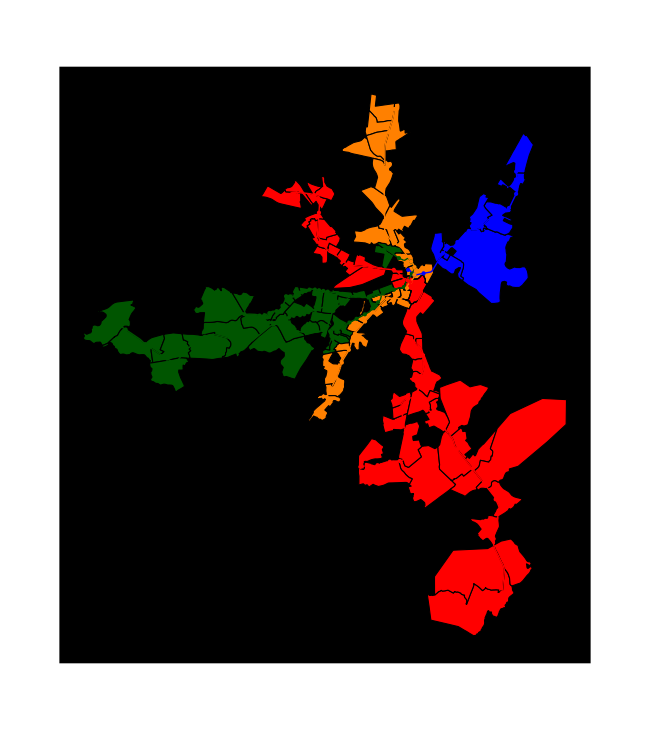
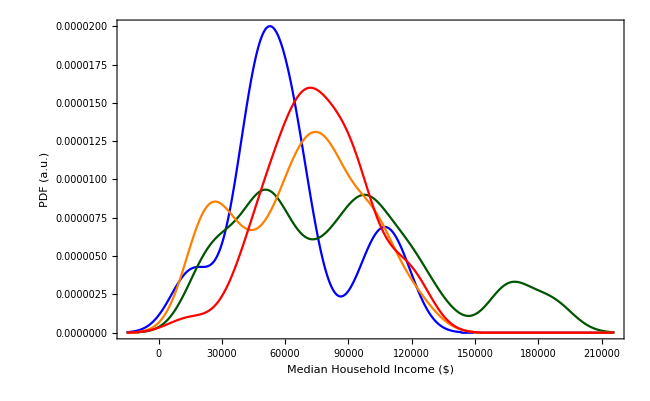

```mathematica
Row[{
GeoGraphics[
{EdgeForm[Black],Thread[{cleanedUpCols,Lookup[censusTractsPolygonsAsc,Keys[KeyDrop[censusTractsPolygonsAsc,980101]][[tractsCrossingLine[#]]]]&/@Keys[lineGraphics]}],
MapThread[{Thick,#1,geometryAssociations["MBTA_ARC"][[cleanedUpRoutesByLine[#2]]]}&,{cleanedUpCols,cleanedUpRoutesByLine//Keys}],
MapThread[{PointSize[Large],#1,Point[cleanedUpStationsByLine[#2][[All,3]]]}&,{cleanedUpCols,cleanedUpStationsByLine//Keys}]},GeoBackground->None,ImageSize->650],SmoothHistogram[DeleteCases[Lookup[AssociationThread[data[[All,3]]->data[[All,12]]],Keys[KeyDrop[censusTractsPolygonsAsc,980101]][[tractsCrossingLine[#]]]]&/@Keys[lineGraphics],"",{2}],10000,PlotStyle->cleanedUpCols,Frame->True,ImageSize->650,FrameLabel->{"Median Household Income ($)","PDF (a.u.)"},BaseStyle->18]}]
```

### Unfolding Lines

```mathematica
lineGraphicsTmp=MapAt[Join[#[[1]],#[[2]]]&,lineGraphics,{"BLUE",-1}];
```

```mathematica
order=<|
"ORANGE"->Join[Range[2,15],{22,16,1},Range[21,17,-1]],
"BLUE"->Join[{1},Range[5,2,-1],{6}],
"RED-B"->Reverse@Join[{1,6,5},{7,8},{15,16},{10,11},{2}],
"RED-A"->Reverse@Join[{1,6,5},{7},{9,4},{12,13},{3,14}],
"GREEN-B"->Reverse@Join[{17,15},{10,9},{11},{5,12}],
"GREEN-C"->Reverse@Join[{17,15},{10,9},{11},{8},{4,14}],
"GREEN-D"->Reverse@Join[{17,15},{10,9},{11},{8},{3,1,13}],
"GREEN-E"->Reverse@Join[{17,15},{10,9},{7,16,6}]
|>;
```

```mathematica
Keys[orderedLineGraphics=KeySort@<|
"ORANGE"->Line[DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["ORANGE"],{2}][[order["ORANGE"]]])]],
"BLUE"->Line[DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["BLUE"],{2}][[order["BLUE"]]])]],
"RED-B"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["RED"],{2}][[order["RED-B"]]])]],
"RED-A"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["RED"],{2}][[order["RED-A"]]])]],
"GREEN-B"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-B"]]])]],
"GREEN-C"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-C"]]])]],
"GREEN-D"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-D"]]])]],
"GREEN-E"->Line[Reverse@DeleteDuplicates[Join@@(Map[Reverse,lineGraphicsTmp["GREEN"],{2}][[order["GREEN-E"]]])]]|>]
```

{BLUE,GREEN-B,GREEN-C,GREEN-D,GREEN-E,ORANGE,RED-A,RED-B}

```mathematica
orderedCols=Join[{Blue},Rest[ResourceFunction["ColorBrewerData"]["Greens",5]],{Orange},Rest[ResourceFunction["ColorBrewerData"]["Reds",3]]]
```

{RGBColor[0, 0, 1],RGBColor[Rational[62, 85], Rational[76, 85], Rational[179, 255]],RGBColor[Rational[116, 255], Rational[196, 255], Rational[118, 255]],RGBColor[Rational[49, 255], Rational[163, 255], Rational[28, 85]],RGBColor[0, Rational[109, 255], Rational[44, 255]],RGBColor[1, 0.5, 0],RGBColor[Rational[84, 85], Rational[146, 255], Rational[38, 85]],RGBColor[Rational[74, 85], Rational[3, 17], Rational[38, 255]]}

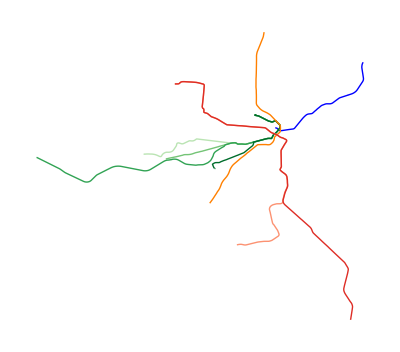

```mathematica
Graphics[{Thick,Thread[{orderedCols,Values[orderedLineGraphics]}]}]
```

```mathematica
nearestLines=Nearest@*First/@orderedLineGraphics;
```

```mathematica
cleanedUpStationsByLineFinelyGrained=Join[cleanedUpStationsByLine,
<|"RED-A"->Select[cleanedUpStationsByLine["RED"],MemberQ[{"Alewife","Davis","Porter","Harvard","Central","Kendal/MIT","Charles/MGH","Park Street","Downtown Crossing","South Station","Broadway","Andrew","JFK/UMass","Savin Hill","Fields Corner","Shawmut","Ashmont","Cedar Grove","Butler","Milton","Central Avenue","Valley Road","Capen Street","Mattapan"},#[[1]]]&],
"RED-B"->Select[cleanedUpStationsByLine["RED"],MemberQ[{"Alewife","Davis","Porter","Harvard","Central","Kendal/MIT","Charles/MGH","Park Street","Downtown Crossing","South Station","Broadway","Andrew","JFK/UMass","North Quincy","Wollaston","Quincy Center","Quincy Adams","Braintree"},#[[1]]]&],

"GREEN-B"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Hynes Convention Center","Kenmore","Blandford Street","Boston University East","Boston University Central","Boston University West","Saint Paul Street","Pleasant Street","Babcock Street","Packards Corner","Harvard Avenue","Griggs Street","Allston Street","Warren Street","Washington Street","Sutherland Road","Chiswick Road","Chestnut Hill Avenue","South Street","Boston College"},#[[1]]]&],
"GREEN-C"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Hynes Convention Center","Kenmore","Saint Marys Street","Hawes Street","Kent Street",(*"Saint Paul Street",*)"Coolidge Corner","Summit Ave/Winchester St","Brandon Hall","Fairbanks Street","Washington Square","Tappan Street","Dean Road","Englewood Avenue","Cleveland Circle"},#[[1]]]&],
"GREEN-D"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Hynes Convention Center","Kenmore","Fenway Park","Longwood","Brookline Village","Brookline Hills","Beaconsfield","Reservoir","Chestnut Hill","Newton Centre","Newton Highlands","Eliot","Waban","Woodland","Riverside"},#[[1]]]&],
"GREEN-E"->Select[cleanedUpStationsByLine["GREEN"],MemberQ[{"Lechmere","Science Park","North Station","Haymarket","Government Center","Park Street","Boylston","Arlington","Copley","Prudential","Symphony","Northeastern","Museum Of Fine Arts","Longwood Medical Area","Brigham Circle","Fenwood Road","Mission Park","Riverway","Back Of The Hill","Heath Street"},#[[1]]]&]
|>];
```

```mathematica
lineAtStation[line_,stationIndex_]:=Block[{station,pos,name,pt},
station=cleanedUpStationsByLineFinelyGrained[line][[stationIndex]];
pt=Reverse[station[[3,1]]];
name=station[[1]];
pos=First[FirstPosition[First[orderedLineGraphics[line]],First@nearestLines[line][pt,1]]];
name->Line[Take[First[orderedLineGraphics[line]],pos]]
]
```

```mathematica
Length/@cleanedUpStationsByLineFinelyGrained
```

<|BLUE→12,GREEN→65,ORANGE→20,RED→29,RED-A→23,RED-B→17,GREEN-B→29,GREEN-C→23,GREEN-D→24,GREEN-E→20|>

```mathematica
stations["RED-A"]=Sort[((ArcLength/@Association[lineAtStation["RED-A",#]&/@Range[23]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
stations["RED-B"]=Sort[((ArcLength/@Association[lineAtStation["RED-B",#]&/@Range[17]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
stations["BLUE"]=Sort[((ArcLength/@Association[lineAtStation["BLUE",#]&/@Range[12]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
stations["ORANGE"]=Sort[((ArcLength/@Association[lineAtStation["ORANGE",#]&/@Range[20]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
stations["GREEN-B"]=Sort[((ArcLength/@Association[lineAtStation["GREEN-B",#]&/@Range[29]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
stations["GREEN-C"]=Sort[((ArcLength/@Association[lineAtStation["GREEN-C",#]&/@Range[23]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
stations["GREEN-D"]=Sort[((ArcLength/@Association[lineAtStation["GREEN-D",#]&/@Range[24]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
stations["GREEN-E"]=Sort[((ArcLength/@Association[lineAtStation["GREEN-E",#]&/@Range[20]])/._ArcLength:>0)/ArcLength[orderedLineGraphics["GREEN-E"]]];
```

```mathematica
trackLength=Normalize[ArcLength/@orderedLineGraphics,Min]
```

<|BLUE→1.06321,GREEN-B→1.54599,GREEN-C→1.30488,GREEN-D→2.57597,GREEN-E→1.,ORANGE→1.83468,RED-A→2.56284,RED-B→3.0585|>

```mathematica
connector[y1_,y2_,{x0_,x1_,length_}]:=
Append[Prepend[Table[{t+x0,y1+(y2-y1) LogisticSigmoid[Rescale[t,{x1-3/8,x1+3/8},{-25,25}]]},{t,Subdivide[x1-3/8,x1+3/8,50]}],{x0,y1}],{x0+length,y2}]
```

```mathematica
medianIncomeSparkLine[line_,{x0_,y0_}]:=DeleteCases[Thread[{x0+stations[line]//Values,y0+Rescale[Lookup[AssociationThread[data[[All,3]]->data[[All,12]]],Lookup[stationTract[line],stations[line]//Keys]]/.""->Missing[],{0,200000},{0,0.5}]}],{a_,Plus[_,Times[_,_Missing]]}]
```

```mathematica
stationTract=AssociationThread[#[[All,1]]->Keys[censusTractsRegionMembers][[First/@SortBy[Position[Through[Values[censusTractsRegionMembers][#[[All,3,1]]]],True],Last]]]]&/@KeyDrop[cleanedUpStationsByLineFinelyGrained,{"GREEN","RED"}];
```

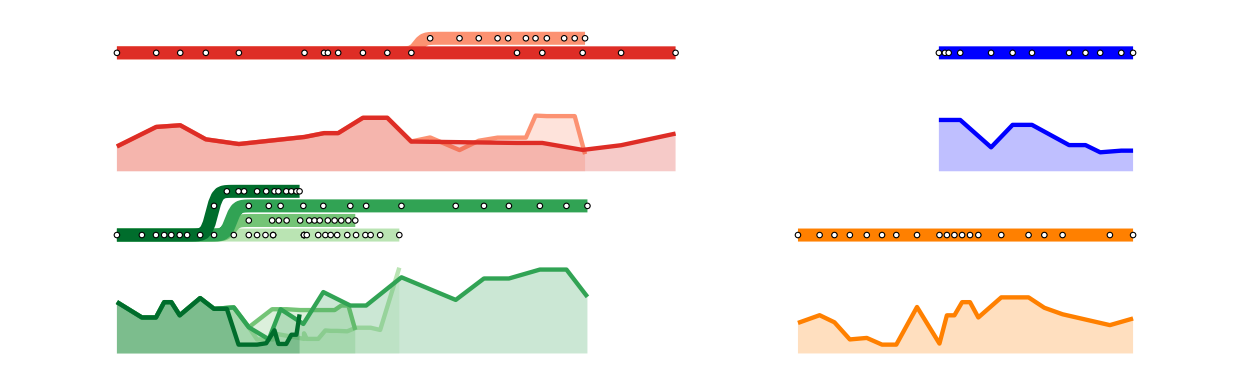

```mathematica
Graphics[{Thickness[0.0075],CapForm["Round"],
Thread[{orderedCols,
{
{Line@connector[0,0,{4.5,0.51,trackLength["BLUE"]}],Thickness[0.0025],Line[medianIncomeSparkLine["BLUE",{4.5,-0.65}]],Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["BLUE",{4.5,-0.65}],{4.5,-0.65}],{{4.5+trackLength["BLUE"],-0.65},{4.5,-0.65}}]]},

{Line@connector[-1,-1,{0,0.625,trackLength["GREEN-B"]}],Thickness[0.0025],Line[medianIncomeSparkLine["GREEN-B",{0,-1.65}]],
Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["GREEN-B",{0,-1.65}],{0,-1.65}],{{trackLength["GREEN-B"],-1.65},{0,-1.65}}]]
},

{Line@connector[-1,-1+0.08,{0,0.625,trackLength["GREEN-C"]}],Thickness[0.0025],Line[medianIncomeSparkLine["GREEN-C",{0,-1.65}]],
Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["GREEN-C",{0,-1.65}],{0,-1.65}],{{trackLength["GREEN-C"],-1.65},{0,-1.65}}]]},

{Line@connector[-1,-1+2 0.08,{0,0.625,trackLength["GREEN-D"]}],Thickness[0.0025],Line[medianIncomeSparkLine["GREEN-D",{0,-1.65}]],
Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["GREEN-D",{0,-1.65}],{0,-1.65}],{{trackLength["GREEN-D"],-1.65},{0,-1.65}}]]},

{Line@connector[-1,-1+3 0.08,{0,0.52,trackLength["GREEN-E"]}],Thickness[0.0025],Line[medianIncomeSparkLine["GREEN-E",{0,-1.65}]],
Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["GREEN-E",{0,-1.65}],{0,-1.65}],{{trackLength["GREEN-E"],-1.65},{0,-1.65}}]]},

{Line@connector[-1,-1,{4.5+trackLength["BLUE"]-trackLength["ORANGE"],0.51,trackLength["ORANGE"]}],Thickness[0.0025],Line@medianIncomeSparkLine["ORANGE",{4.5+trackLength["BLUE"]-trackLength["ORANGE"],-1.65}],
Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["ORANGE",{4.5+trackLength["BLUE"]-trackLength["ORANGE"],-1.65}],{4.5+trackLength["BLUE"]-trackLength["ORANGE"],-1.65}],{{4.5+trackLength["BLUE"],-1.65},{4.5+trackLength["BLUE"]-trackLength["ORANGE"],-1.65}}]]},

{Line@connector[0,0.08,{0,1.65,trackLength["RED-A"]}],Thickness[0.0025],Line[medianIncomeSparkLine["RED-A",{0,-0.65}]],
Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["RED-A",{0,-0.65}],{0,-0.65}],{{trackLength["RED-A"],-0.65},{0,-0.65}}]]},

{Line@connector[0,0,{0,1.65,trackLength["RED-B"]}],Thickness[0.0025],Line[medianIncomeSparkLine["RED-B",{0,-0.65}]],
Opacity[0.25],Polygon[Join[Prepend[medianIncomeSparkLine["RED-B",{0,-0.65}],{0,-0.65}],{{trackLength["RED-B"],-0.65},{0,-0.65}}]]}
}}],
{EdgeForm[Black],FaceForm[White],
Disk[{#+4.5+trackLength["BLUE"]-trackLength["ORANGE"],-1},0.015]&/@Values[stations["ORANGE"]],
Disk[{#+4.5,0},0.015]&/@Values[stations["BLUE"]],
Disk[{#,0},0.015]&/@Values[stations["RED-B"]],
Disk[{#,0.08},0.015]&/@Values[Select[stations["RED-A"],#>1.65&]],
Disk[{#,-1},0.015]&/@Values[stations["GREEN-B"]],
Disk[{#,-1+0.08},0.015]&/@Values[Select[stations["GREEN-C"],#>0.65&]],
Disk[{#,-1+2 0.08},0.015]&/@Values[Select[stations["GREEN-D"],#>0.65&]],
Disk[{#,-1+3 0.08},0.015]&/@Values[Select[stations["GREEN-E"],#>0.6&]],
Disk[{#,-1+2 0.08},0.015]&/@Values[Select[stations["GREEN-E"],0.6>#>0.5&]]}
},ImageSize->1250]
```